```mathematica
Clear["Global`*"];
```

```mathematica
$Version
```

12.1.0 for Linux x86 (64-bit) (March 14, 2020)

# Demo file for ManeParse Package Version 5.0

### Version 5.0 18 October 2019 Comments and questions to: Eric Godat egodat@smu.edu Ben Clark dbclark@smu.edu Fred Olness olness@physics.smu.edu

## Set Directory

#### This example notebook is written with relative directories and is intended to be run within the folder extracted from the tarball. Uncomment and modify the code below to set a different directory for the LHA files.

```mathematica
(* This just drops the leading path info to make the list of files easier to read *)
dropPath=Take[(FileNameSplit /@ # ) //Transpose,-1][[1]]&;
```

```mathematica
NotebookDirectory[];
here=NotebookDirectory[]
```

C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\

```mathematica
(* If there is a problem with the Mathematica working directory, 
you can enter it manually here *)
SetDirectory[here]
```

C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo

```mathematica
(* This shows what files should be in this main directory *)
FileNames["*.*",here] //dropPath
```

{Demo5.nb,Demo5.pdf,figs4paper_v5.nb,figs4paper_v5.pdf,GeneratingCTEQ6L1PDF.nb,MakeDemo.py,ManeParse_v2.pdf,manual_v5.nb,manual_v5.pdf,noe2.perl,User.pdf}

## Setup Other Directories

```mathematica
dirPackages=here<>"/MP_packages";
```

```mathematica
dirFilesLHA=here<>"./PDFDIR/LHA";
dirCT10=dirFilesLHA<>"/CT10";
dirMSTW=dirFilesLHA<>"/MSTW2008lo68cl";
dirNNPDF=dirFilesLHA<>"/NNPDF30_nlo_as_0118";
dirCTEQ6L1=dirFilesLHA<>"/CETQ6L1";
FileNames["*",dirFilesLHA] //dropPath
```

{CT10,CTEQ6L1,MSTW2008lo68cl,NNPDF30_nlo_as_0118}

```mathematica
dirFilesPDS=here<>"./PDFDIR/PDS";
dirCT10pds = dirFilesPDS<>"/ct10.pds";
dirCTEQ66 = dirFilesPDS<>"/ctq66m.pds";
FileNames["*",dirFilesPDS] //dropPath
```

{ct10.pds,ctq66m.pds}

```mathematica
dirPackages
FileNames["*",dirPackages]//dropPath
```

C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\/MP_packages

{pdfCalc.m,pdfErrors.m,pdfParseCTEQ.m,pdfParseLHA.m,README_V05.TXT}

```mathematica
FileNames["*.dat",dirCT10]//dropPath //Short
```

{CT10_0000.dat,CT10_0001.dat,CT10_0002.dat,CT10_0003.dat,«46»,CT10_0050.dat,CT10_0051.dat,CT10_0052.dat}

## Load the package

#### Loading the main package provides many useful functions

```mathematica
Get[dirPackages<>"/pdfParseLHA.m"]
```

===============================================================

- pdfParseLHA -

Version:  5.0: April 2021

Authors: E.J. Godat, D.B. Clark & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

SetDelayed::write: Tag pdfParseLHA in pdfParseLHA[fileNameInfo_,fileNameData_,verbose_:True] is Protected.

SetDelayed::write: Tag pdfFamilyParseLHA in pdfFamilyParseLHA[path_?StringQ,type_:*.dat] is Protected.

```mathematica
Get[dirPackages<>"/pdfParseCTEQ.m"]
```

===============================================================

- pdfParseCTEQ -

Version:  5.0:  April 2021

Authors: D.B. Clark, E.J. Godat & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

SetDelayed::write: Tag pdfParseCTEQ in pdfParseCTEQ[filename_?StringQ,verbose_:True] is Protected.

SetDelayed::write: Tag pdfFamilyParseCTEQ in pdfFamilyParseCTEQ[path_?StringQ,type_:*.pds] is Protected.

```mathematica
Get[dirPackages<>"/pdfErrors.m"]
```

===============================================================

- pdfErrors -

Version:  5.0; April 2021

Authors: D.B. Clark, E.J. Godat & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

SetDelayed::write: Tag pdfFamilyFunction in pdfFamilyFunction[family_?ListQ,inputFunc_] is Protected.

SetDelayed::write: Tag pdfHessianError in pdfHessianError[ff_?ListQ,method_:sym] is Protected.

SetDelayed::write: Tag pdfHessianError in pdfHessianError[family_?ListQ,ipart_,x_,q_,method_:sym] is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

#### All functions begin with ' pdf'. To obtain a list of available functions, type the command '?pdf*'.

```mathematica
?pdf*
```

## Individual file manipulation

#### Individual files in either LHA or PDS format can be parsed using the functions loaded from the packages. Here we demonstrate the LHA parsing function

```mathematica
?pdfParseLHA
```

```mathematica
datfiles=FileNames["*.dat","C:\\Users\\novar\\Downloads\\ManeParse5_Demo\\ManeParse5_Demo\\PDFDIR\\LHA\\CTEQ6L1\\"];(* This is a set of LHA PDFs *)
infofile=FileNames["*.info","C:\\Users\\novar\\Downloads\\ManeParse5_Demo\\ManeParse5_Demo\\PDFDIR\\LHA\\CTEQ6L1\\"];(* This is the associated info file *)
datfiles
```

```mathematica
infofile
```

{C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\PDFDIR\LHA\CTEQ6L1\cteq6l1.info}

```mathematica
dirCTEQ6L1
```

C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\./PDFDIR/LHA/CETQ6L1

```mathematica
sample=pdfParseLHA[infofile[[1]],datfiles[[1]]]
```

Successfully read C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\PDFDIR\LHA\CTEQ6L1\cteq6l1.info.

Successfully read C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\PDFDIR\LHA\CTEQ6L1\cteq6l1_0000.dat.

56

#### Calling the pdfSetList variable will give a key to the data files in memory. The information is displayed as: {SetNumber,FileName, maxFlavor, numberValence}

```mathematica
pdfSetList//TableForm
```

1 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\./PDFDIR/LHA/CT10\CT10_0000.dat | 5 | n/a
2 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\./PDFDIR/LHA/CT10\CT10_0001.dat | 5 | n/a
3 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0000.dat | 5 | n/a
4 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0001.dat | 5 | n/a
5 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0002.dat | 5 | n/a
6 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0003.dat | 5 | n/a
7 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0004.dat | 5 | n/a
8 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0005.dat | 5 | n/a
9 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0006.dat | 5 | n/a
10 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0007.dat | 5 | n/a
11 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0008.dat | 5 | n/a
12 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0009.dat | 5 | n/a
13 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0010.dat | 5 | n/a
14 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0011.dat | 5 | n/a
15 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0012.dat | 5 | n/a
16 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0013.dat | 5 | n/a
17 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0014.dat | 5 | n/a
18 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0015.dat | 5 | n/a
19 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0016.dat | 5 | n/a
20 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0017.dat | 5 | n/a
21 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0018.dat | 5 | n/a
22 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0019.dat | 5 | n/a
23 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0020.dat | 5 | n/a
24 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0021.dat | 5 | n/a
25 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0022.dat | 5 | n/a
26 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0023.dat | 5 | n/a
27 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0024.dat | 5 | n/a
28 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0025.dat | 5 | n/a
29 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0026.dat | 5 | n/a
30 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0027.dat | 5 | n/a
31 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0028.dat | 5 | n/a
32 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0029.dat | 5 | n/a
33 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0030.dat | 5 | n/a
34 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0031.dat | 5 | n/a
35 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0032.dat | 5 | n/a
36 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0033.dat | 5 | n/a
37 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0034.dat | 5 | n/a
38 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0035.dat | 5 | n/a
39 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0036.dat | 5 | n/a
40 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0037.dat | 5 | n/a
41 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0038.dat | 5 | n/a
42 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0039.dat | 5 | n/a
43 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0040.dat | 5 | n/a
44 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0041.dat | 5 | n/a
45 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0042.dat | 5 | n/a
46 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0043.dat | 5 | n/a
47 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0044.dat | 5 | n/a
48 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0045.dat | 5 | n/a
49 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0046.dat | 5 | n/a
50 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0047.dat | 5 | n/a
51 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0048.dat | 5 | n/a
52 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0049.dat | 5 | n/a
53 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0050.dat | 5 | n/a
54 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0051.dat | 5 | n/a
55 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0052.dat | 5 | n/a
56 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\PDFDIR\LHA\CTEQ6L1\cteq6l1_0000.dat | 5 | n/a

#### Files can be added to memory without a name. All files can be called by their set numbers.

```mathematica
pdfParseLHA[infofile[[1]],datfiles[[1]]]
```

Successfully read C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\PDFDIR\LHA\CTEQ6L1\cteq6l1.info.

Successfully read C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\PDFDIR\LHA\CTEQ6L1\cteq6l1_0000.dat.

57

```mathematica
pdfSetList//TableForm
```

1 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\./PDFDIR/LHA/CT10\CT10_0000.dat | 5 | n/a
2 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\./PDFDIR/LHA/CT10\CT10_0001.dat | 5 | n/a
3 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0000.dat | 5 | n/a
4 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0001.dat | 5 | n/a
5 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0002.dat | 5 | n/a
6 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0003.dat | 5 | n/a
7 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0004.dat | 5 | n/a
8 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0005.dat | 5 | n/a
9 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0006.dat | 5 | n/a
10 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0007.dat | 5 | n/a
11 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0008.dat | 5 | n/a
12 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0009.dat | 5 | n/a
13 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0010.dat | 5 | n/a
14 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0011.dat | 5 | n/a
15 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0012.dat | 5 | n/a
16 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0013.dat | 5 | n/a
17 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0014.dat | 5 | n/a
18 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0015.dat | 5 | n/a
19 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0016.dat | 5 | n/a
20 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0017.dat | 5 | n/a
21 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0018.dat | 5 | n/a
22 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0019.dat | 5 | n/a
23 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0020.dat | 5 | n/a
24 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0021.dat | 5 | n/a
25 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0022.dat | 5 | n/a
26 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0023.dat | 5 | n/a
27 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0024.dat | 5 | n/a
28 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0025.dat | 5 | n/a
29 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0026.dat | 5 | n/a
30 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0027.dat | 5 | n/a
31 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0028.dat | 5 | n/a
32 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0029.dat | 5 | n/a
33 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0030.dat | 5 | n/a
34 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0031.dat | 5 | n/a
35 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0032.dat | 5 | n/a
36 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0033.dat | 5 | n/a
37 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0034.dat | 5 | n/a
38 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0035.dat | 5 | n/a
39 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0036.dat | 5 | n/a
40 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0037.dat | 5 | n/a
41 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0038.dat | 5 | n/a
42 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0039.dat | 5 | n/a
43 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0040.dat | 5 | n/a
44 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0041.dat | 5 | n/a
45 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0042.dat | 5 | n/a
46 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0043.dat | 5 | n/a
47 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0044.dat | 5 | n/a
48 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0045.dat | 5 | n/a
49 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0046.dat | 5 | n/a
50 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0047.dat | 5 | n/a
51 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0048.dat | 5 | n/a
52 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0049.dat | 5 | n/a
53 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0050.dat | 5 | n/a
54 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0051.dat | 5 | n/a
55 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10_0052.dat | 5 | n/a
56 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\PDFDIR\LHA\CTEQ6L1\cteq6l1_0000.dat | 5 | n/a
57 | C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\PDFDIR\LHA\CTEQ6L1\cteq6l1_0000.dat | 5 | n/a

#### Open and parse single files in any order. You may assign names to each pdf set. Each PDF set is identified by a SetNumber.

## Batch file manipulation

#### Resetting memory can be accomplished with the pdfReset command.

```mathematica
pdfReset[]
```

Default Mathematica interpolator will be used.

All internal variables have been reset.

#### The set list is now empty.

```mathematica
pdfSetList //TableForm
```

{}

#### The pdfFamilyParseLHA command can be used to store a family of LHA info and dat files in memory. The function returns a list of values that can be associated with the family.

```mathematica
?pdfFamilyParseLHA
```

#### First we import the ct10 dat files. The family will include the info file, the central value(set #1) and 52 eigenvector error sets. The family name can be defined at this point.

```mathematica
cteq6l1=pdfFamilyParseLHA["C:\\Users\\novar\\Downloads\\ManeParse5_Demo\\ManeParse5_Demo\\PDFDIR\\LHA\\CTEQ6L1\\","*.dat"]
```

Successfully read C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\PDFDIR\LHA\CTEQ6L1\cteq6l1.info.

Included 1 files in the PDF family.

{58}

## Test PDFs

#### The function “pdf” is left to be defined by the user. Access to the PDF of the set is given by pdfFunction. The function has the canonical form: pdfFunction[setNumber,flavorNumber,x,Q]. If the function is not defined, pdfFunction returns NULL.

```mathematica
?pdfFunction
```

```mathematica
pdfFunction[1,1,.1,10]
```

3.96968

```mathematica
Clear[pdf]
pdf[iset_?IntegerQ,ipart_?IntegerQ,x_?NumericQ,q_?NumericQ]:=pdfFunction[iset,ipart,x,q]
```

```mathematica
pdf[1,1,.1,10]
pdf[2,1,0.1,10]

centralvalue = 1;

pdf[centralvalue,1,0.1,10]
```

3.96968

3.95809

3.96968

### Check Timing :

```mathematica
Table[pdf[58,0,RandomReal[],10.],{i,1,1000}]  //Timing //First
```

0.578125

```mathematica
Table[pdf[58,0,1/i,10.],{i,1.,1000}]  //Timing //First
```

0.53125

#### Check sum rule:

```mathematica
Off[NIntegrate::izero]
Off[NIntegrate::ncvb]
q0=2.0;
iset0=58;
```

```mathematica
(* This can take a while *)
tab= Table[ NIntegrate[ x pdf[iset0,ipart,x,q0],{x,0,1}],{ipart,-5,5,1}];//Timing
Plus @@ tab
```

{4.28125,Null}

0.999917

```mathematica
flavorlist={};
```

```mathematica
For[i=-5,i≤5,i++,AppendTo[flavorlist,pdfFlavor[i]];]
```

```mathematica
flavorlist
```

{bbar,cbar,sbar,ubar,dbar,gluon,down,up,strange,charm,bottom}

```mathematica
{Range[-5,5],flavorlist,Round[100 tab]} //Transpose //Grid[#,Frame->All]&
```

-5 | bbar | 0
-4 | cbar | 0
-3 | sbar | 2
-2 | ubar | 3
-1 | dbar | 4
0 | gluon | 44
1 | down | 15
2 | up | 31
3 | strange | 2
4 | charm | 0
5 | bottom | 0

## Example: Plotting Single Functions

#### First we find the minimum value of x for our pdf family.

```mathematica
?pdfXmin
```

```mathematica
xMin=pdfXmin[1]
```

1.×10^-8

#### We will produce plots of x*pdf(x,Q) for all flavors with the central value in red and the first error set in green. The flavor can be called with the command pdfFlavor[flavor].

```mathematica
q0=10;
centralvalue=58;
errorvalue=2;
```

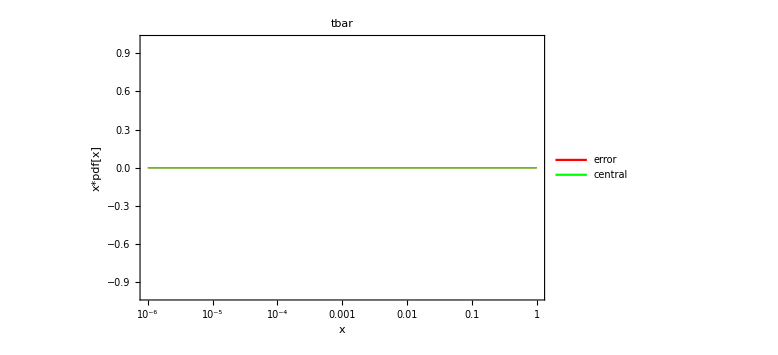

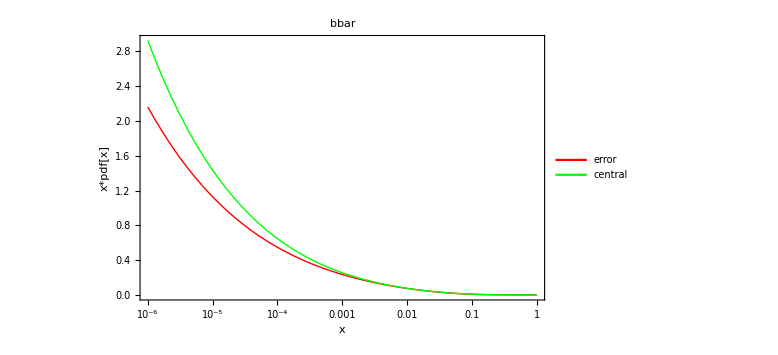

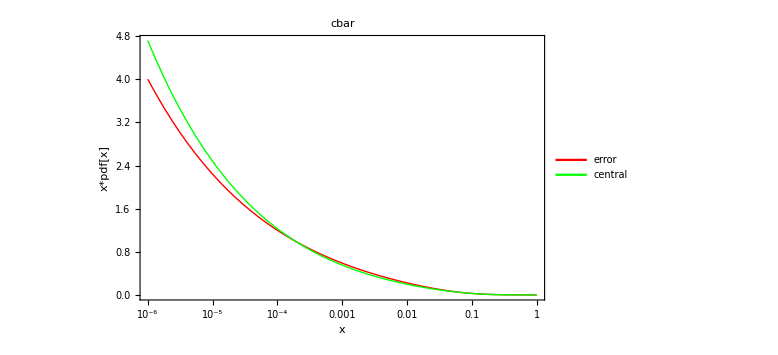

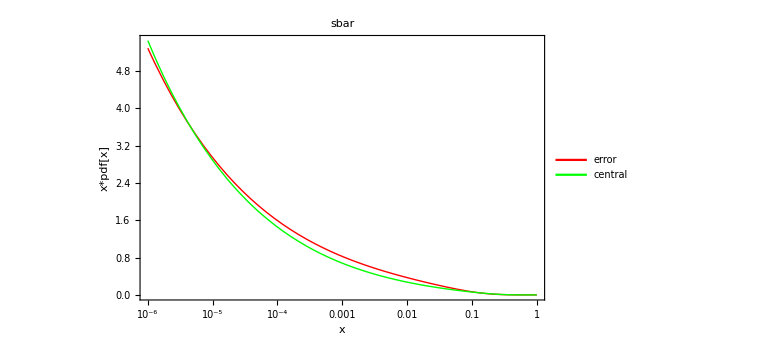

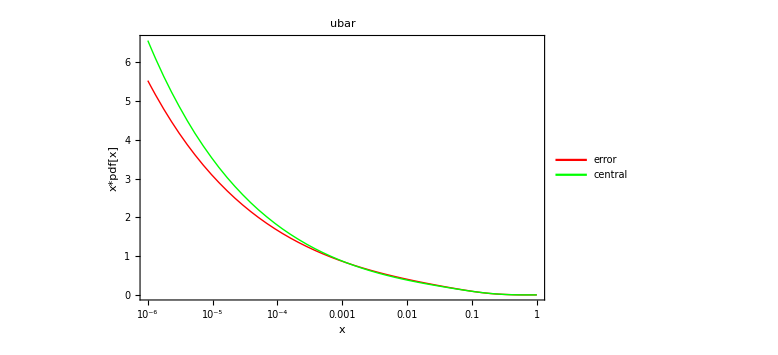

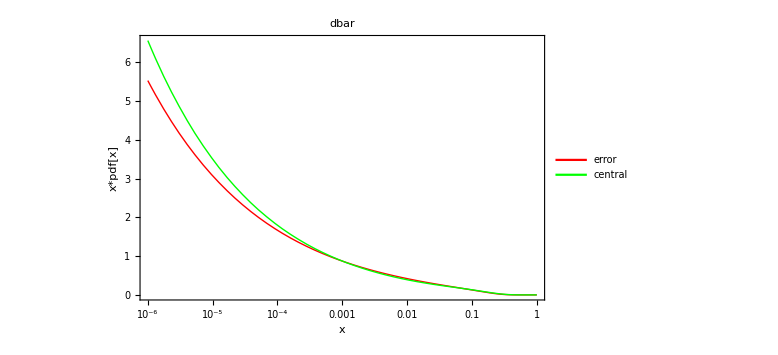

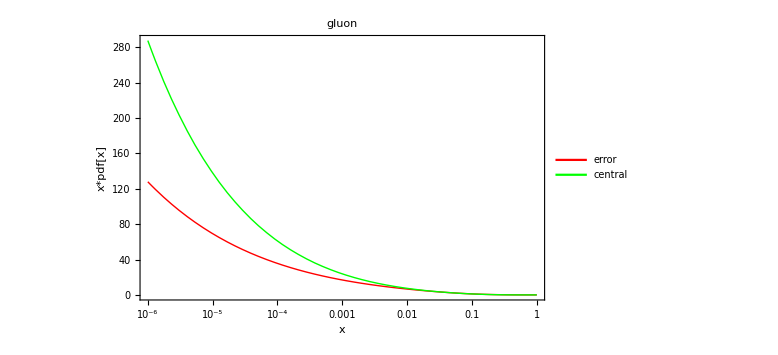

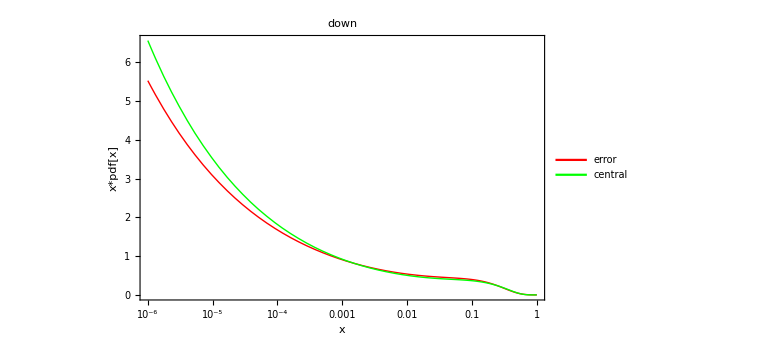

```mathematica
For[i=-6,i≤6,i++,
LogLinearPlot[x {pdf[errorvalue,i,x,q0],pdf[centralvalue,i,x,q0]}//Evaluate ,{x,xMin*100,1},
PlotStyle->{Directive[Red,Thick],Directive[Green,Thick]},
PlotLabel->pdfFlavor[i] ,
FrameLabel->{"x","x*pdf[x]"},
ImageSize->Large,
PlotRange->All,
Frame->True,
BaseStyle->{FontWeight->"Bold",FontSize->12},
GridLines->Automatic,
PlotLegends->Placed[{"error","central"},{0.1,0.18}]] //Print
]
```

## PLAY

#### First we find the minimum value of x for our pdf family.

```mathematica
?pdfXmin
```

```mathematica
xMin=pdfXmin[1]
```

1.×10^-8

```mathematica
pdfQmin[1]
```

pdfQmin[1]

```mathematica
pdfGetInfo[58] //TableForm
```

SetDesc→ "CTEQ6L1 - LO with LO alpha_s. CTEQ6 parameterization. mem=0 => central PDF"
SetIndex→10042
Authors→ J. Pumplin, D.R. Stump, J. Huston, H.L. Lai, P. Nadolsky, W.K. Tung
Reference→ hep-ph/0201195
Format→ lhagrid1
DataVersion→4
NumMembers→1
Particle→2212
Flavors→{-5,-4,-3,-2,-1,1,2,3,4,5,21}
OrderQCD→0
ForcePositive→ 1
FlavorScheme→ variable
NumFlavors→5
XMin→1/1000000
XMax→1
QMin→1.3
QMax→10000
MZ→91.1876
MUp→ 0
MDown→ 0
MStrange→ 0
MCharm→ 1.3
MBottom→ 4.5
MTop→ 180
AlphaS_MZ→ 0.129783
AlphaS_OrderQCD→ 0
AlphaS_Type→ ipol
AlphaS_Qs→{1.3,1.56045,1.87309,2.24836,2.69881,3.23951,3.88854,4.66761,5.60275,6.72526,8.07265,9.68999,11.6314,13.9617,16.7589,20.1165,24.1468,28.9846,34.7916,41.762,50.129,60.1722,72.2277,86.6983,91.1876,104.068,124.918,149.945,179.987,216.046,259.331,311.287,373.653,448.514,538.373,646.236,775.708,931.119,1117.67,1341.59,1610.38,1933.01,2320.29,2785.15,3343.15,4012.95,4816.94,5782.,6940.42,8330.91,10000.}
AlphaS_Vals→{0.418947,0.380353,0.348271,0.321179,0.297998,0.277938,0.260409,0.245192,0.23249,0.22104,0.210664,0.201219,0.192584,0.18466,0.177362,0.170619,0.16437,0.158563,0.153152,0.148098,0.143367,0.138929,0.134757,0.130829,0.129783,0.127123,0.123622,0.120308,0.117167,0.114186,0.111353,0.108657,0.106088,0.103638,0.101299,0.099063,0.0969235,0.0948746,0.0929104,0.091026,0.0892165,0.0874775,0.085805,0.0841952,0.0826448,0.0811504,0.0797091,0.0783181,0.0769748,0.0756769,0.0744219}
AlphaS_Lambda4→ 0.215
AlphaS_Lambda5→ 0.165

#### We will produce plots of x*pdf(x,Q) for all flavors with the central value in red and the first error set in green. The flavor can be called with the command pdfFlavor[flavor].

```mathematica
q0=1.3;
centralvalue=58;
errorvalue=2;
```

```mathematica
q0=1.3;

For[i=-6,6≤1,i++,
LogLinearPlot[ {pdf[errorvalue,i,x,q0],pdf[centralvalue,i,x,q0]}//Evaluate ,{x,xMin*10^3,1},
PlotStyle->{Directive[Red,Thick],Directive[Green,Thick]},
PlotLabel->pdfFlavor[i] ,
FrameLabel->{"x","pdf[x]"},
ImageSize->Large,
PlotRange->All,
Frame->True,
BaseStyle->{FontWeight->"Bold",FontSize->12},
GridLines->Automatic,
PlotLegends->Placed[{"error","central"},{0.1,0.18}]] //Print
]
```

## Using pdfGetXlist and pdfGetQlist

#### The x and Q grids can be directly read from the stored PDFs.

```mathematica
iset=1;
```

```mathematica
pdfGetQlist[iset]
```

{{1.3,1.50159,1.75516,2.07811,2.49494,3.04086,3.76712,4.74999,6.23105,8.37433,11.5549,16.4074,24.0385,36.4364,57.3141,93.8684,160.657,288.438,545.574,1092.35,2326.49,5300.33,12995.,34515.,100000.}}

```mathematica
pdfGetXlist[iset]
```

{{1.×10^-8,1.2414×10^-8,1.54112×10^-8,1.9132×10^-8,2.37512×10^-8,2.94855×10^-8,3.66043×10^-8,4.54417×10^-8,5.64127×10^-8,7.00323×10^-8,8.69398×10^-8,1.07929×10^-7,1.33985×10^-7,1.66332×10^-7,2.06486×10^-7,2.56334×10^-7,3.18214×10^-7,3.95031×10^-7,4.90389×10^-7,6.09206×10^-7,7.56249×10^-7,9.38778×10^-7,1.16535×10^-6,1.44661×10^-6,1.79581×10^-6,2.22938×10^-6,2.76764×10^-6,3.43585×10^-6,4.26537×10^-6,5.29516×10^-6,6.57355×10^-6,8.16054×10^-6,0.0000101306,0.0000125762,0.0000156121,0.0000193806,0.0000240586,0.0000298652,0.0000370727,0.0000460185,0.0000571214,0.0000709007,0.0000880003,0.000109218,0.000135543,0.0001682,0.000208704,0.000258931,0.000321196,0.000398359,0.000493945,0.000612291,0.000758725,0.000939771,0.00116349,0.00143942,0.00177935,0.00219741,0.00271045,0.00333846,0.00410484,0.00503669,0.00616486,0.00752468,0.00915177,0.0110878,0.0133759,0.0160562,0.019169,0.0227509,0.0268334,0.0314404,0.0365886,0.0422866,0.0485349,0.0553271,0.0626598,0.0704985,0.0788306,0.087621,0.0968651,0.106525,0.116574,0.126988,0.137743,0.148809,0.160178,0.171817,0.183716,0.19585,0.208205,0.220764,0.233517,0.246449,0.259568,0.272827,0.286233,0.299777,0.313451,0.327248,0.341159,0.355179,0.369295,0.383515,0.397826,0.412222,0.4267,0.441256,0.455884,0.470576,0.485354,0.50018,0.515067,0.530013,0.545014,0.560068,0.575171,0.590323,0.605521,0.620762,0.636045,0.651369,0.66673,0.682126,0.697558,0.713035,0.728531,0.744058,0.759616,0.775202,0.790813,0.806447,0.822102,0.837776,0.853464,0.869163,0.884866,0.900563,0.916236,0.931854,0.947357,0.962579,0.977049,0.989087,0.995616,0.997992,0.998976,0.999487,0.999795,1.}}

#### The pdfXmin function gives the minimum value of x for the set. pdfFunction can only reliably interpolate down to this value.

```mathematica
pdfXmin[iset]
```

1.×10^-8

```mathematica
pdfGetXlist[iset] //Min
```

1.×10^-8

## Additional user functions

### pdfGetInfo function

#### can be used to show what content from the info file has been read into memory

```mathematica
?pdfGetInfo
```

```mathematica
pdfGetInfo[58]//TableForm
```

SetDesc→ "CTEQ6L1 - LO with LO alpha_s. CTEQ6 parameterization. mem=0 => central PDF"
SetIndex→10042
Authors→ J. Pumplin, D.R. Stump, J. Huston, H.L. Lai, P. Nadolsky, W.K. Tung
Reference→ hep-ph/0201195
Format→ lhagrid1
DataVersion→4
NumMembers→1
Particle→2212
Flavors→{-5,-4,-3,-2,-1,1,2,3,4,5,21}
OrderQCD→0
ForcePositive→ 1
FlavorScheme→ variable
NumFlavors→5
XMin→1/1000000
XMax→1
QMin→1.3
QMax→10000
MZ→91.1876
MUp→ 0
MDown→ 0
MStrange→ 0
MCharm→ 1.3
MBottom→ 4.5
MTop→ 180
AlphaS_MZ→ 0.129783
AlphaS_OrderQCD→ 0
AlphaS_Type→ ipol
AlphaS_Qs→{1.3,1.56045,1.87309,2.24836,2.69881,3.23951,3.88854,4.66761,5.60275,6.72526,8.07265,9.68999,11.6314,13.9617,16.7589,20.1165,24.1468,28.9846,34.7916,41.762,50.129,60.1722,72.2277,86.6983,91.1876,104.068,124.918,149.945,179.987,216.046,259.331,311.287,373.653,448.514,538.373,646.236,775.708,931.119,1117.67,1341.59,1610.38,1933.01,2320.29,2785.15,3343.15,4012.95,4816.94,5782.,6940.42,8330.91,10000.}
AlphaS_Vals→{0.418947,0.380353,0.348271,0.321179,0.297998,0.277938,0.260409,0.245192,0.23249,0.22104,0.210664,0.201219,0.192584,0.18466,0.177362,0.170619,0.16437,0.158563,0.153152,0.148098,0.143367,0.138929,0.134757,0.130829,0.129783,0.127123,0.123622,0.120308,0.117167,0.114186,0.111353,0.108657,0.106088,0.103638,0.101299,0.099063,0.0969235,0.0948746,0.0929104,0.091026,0.0892165,0.0874775,0.085805,0.0841952,0.0826448,0.0811504,0.0797091,0.0783181,0.0769748,0.0756769,0.0744219}
AlphaS_Lambda4→ 0.215
AlphaS_Lambda5→ 0.165

```mathematica
pdfGetInfo[1,"Flavors"]
```

{-5,-4,-3,-2,-1,1,2,3,4,5,21}

### AlphaS functions

```mathematica
alpha=pdfGetInfo[58,"AlphaS_Vals"]
```

{0.418947,0.380353,0.348271,0.321179,0.297998,0.277938,0.260409,0.245192,0.23249,0.22104,0.210664,0.201219,0.192584,0.18466,0.177362,0.170619,0.16437,0.158563,0.153152,0.148098,0.143367,0.138929,0.134757,0.130829,0.129783,0.127123,0.123622,0.120308,0.117167,0.114186,0.111353,0.108657,0.106088,0.103638,0.101299,0.099063,0.0969235,0.0948746,0.0929104,0.091026,0.0892165,0.0874775,0.085805,0.0841952,0.0826448,0.0811504,0.0797091,0.0783181,0.0769748,0.0756769,0.0744219}

```mathematica
?pdfAlphaS
```

```mathematica
qlist=pdfGetQlist[58](*retrieve qlist from the .dat file*)
```

{{1.3,1.56045,1.87309,2.24836,2.69881,3.23951,3.88854,4.66761,5.60275,6.72526,8.07265,9.68999,11.6314,13.9617,16.7589,20.1165,24.1468,28.9846,34.7916,41.762,50.129,60.1722,72.2277,86.6983,104.068,124.918,149.945,179.987,216.047,259.331,311.288,373.653,448.514,538.373,646.236,775.708,931.119,1117.67,1341.59,1610.38,1933.01,2320.29,2785.15,3343.15,4012.95,4816.94,5782.,6940.42,8330.92,10000.}}

```mathematica
pdfAlphaS[58,Flatten[qlist][[1]]]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

TerminatedEvaluation[RecursionLimit]

```mathematica
alpha
Flatten[qlist]
%%//Length
%%//Length
```

{0.418947,0.380353,0.348271,0.321179,0.297998,0.277938,0.260409,0.245192,0.23249,0.22104,0.210664,0.201219,0.192584,0.18466,0.177362,0.170619,0.16437,0.158563,0.153152,0.148098,0.143367,0.138929,0.134757,0.130829,0.129783,0.127123,0.123622,0.120308,0.117167,0.114186,0.111353,0.108657,0.106088,0.103638,0.101299,0.099063,0.0969235,0.0948746,0.0929104,0.091026,0.0892165,0.0874775,0.085805,0.0841952,0.0826448,0.0811504,0.0797091,0.0783181,0.0769748,0.0756769,0.0744219}

{1.3,1.56045,1.87309,2.24836,2.69881,3.23951,3.88854,4.66761,5.60275,6.72526,8.07265,9.68999,11.6314,13.9617,16.7589,20.1165,24.1468,28.9846,34.7916,41.762,50.129,60.1722,72.2277,86.6983,104.068,124.918,149.945,179.987,216.047,259.331,311.288,373.653,448.514,538.373,646.236,775.708,931.119,1117.67,1341.59,1610.38,1933.01,2320.29,2785.15,3343.15,4012.95,4816.94,5782.,6940.42,8330.92,10000.}

51

50

```mathematica
(*For the Q values provided in the .dat file, this checks that the the AlphaS values at those values match those in the .info file*)
(*If they don't match, the alpha value in the info file is dropped. This is done for demonstration purposes*)
For[i=1,i≤Length[Flatten[qlist]],i++,
If[
pdfAlphaS[58,Flatten[qlist][[i]]]≠alpha[[i]],alpha=Drop[alpha,{i}]
]
]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit::reclim will be suppressed during this calculation.

```mathematica
tab1=Transpose[{Flatten[qlist],alpha[[1;;-2]]}]
```

{{1.3,0.418947},{1.56045,0.380353},{1.87309,0.348271},{2.24836,0.321179},{2.69881,0.297998},{3.23951,0.277938},{3.88854,0.260409},{4.66761,0.245192},{5.60275,0.23249},{6.72526,0.22104},{8.07265,0.210664},{9.68999,0.201219},{11.6314,0.192584},{13.9617,0.18466},{16.7589,0.177362},{20.1165,0.170619},{24.1468,0.16437},{28.9846,0.158563},{34.7916,0.153152},{41.762,0.148098},{50.129,0.143367},{60.1722,0.138929},{72.2277,0.134757},{86.6983,0.130829},{104.068,0.129783},{124.918,0.127123},{149.945,0.123622},{179.987,0.120308},{216.047,0.117167},{259.331,0.114186},{311.288,0.111353},{373.653,0.108657},{448.514,0.106088},{538.373,0.103638},{646.236,0.101299},{775.708,0.099063},{931.119,0.0969235},{1117.67,0.0948746},{1341.59,0.0929104},{1610.38,0.091026},{1933.01,0.0892165},{2320.29,0.0874775},{2785.15,0.085805},{3343.15,0.0841952},{4012.95,0.0826448},{4816.94,0.0811504},{5782.,0.0797091},{6940.42,0.0783181},{8330.92,0.0769748},{10000.,0.0756769}}

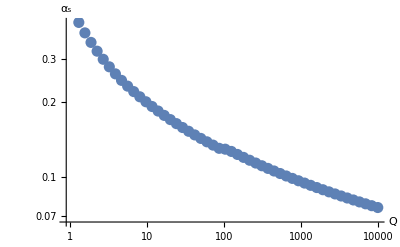

```mathematica
p1=ListLogLogPlot[tab1,AxesLabel->{"Q","α_s"},PlotStyle->{PointSize[.02]}]
```

```mathematica
alphaQ[Q_]:=Interpolation[{Log[#[[1]]],#[[2]]}&/@tab1][Log[Q]]
```

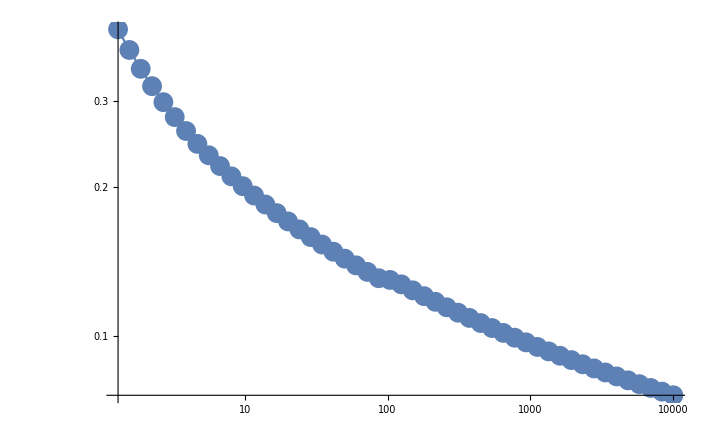

```mathematica
Show[LogLogPlot[alphaQ[Q],{Q,1.3,10^4}],p1]
```

InterpolatingFunction::dmval: Input value {0.000188154} lies outside the range of data in the interpolating function. Extrapolation will be used.

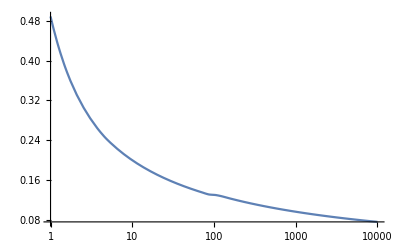

```mathematica
LogLinearPlot[alphaQ[Q],{Q,1,10^4}]
```